# WELP Acoustic Modeling Draft

Abstract
This project aims to explore the propagation of sound in three dimensional regions. We begin by experimenting with acoustic modeling using primitive shapes. After coming up with a working acoustic model, we utilized a depth sensing neural network to extrapolate data from single images. Using this data, we were able to create a boolean region that is representative of the environment being surveyed. We integrated this depth map with our acoustic model to obtain attenuation coefficients which were applied to sample audio. Throughout the process, we were able to come across interesting visualizations, learn about the basic physics behind acoustics and explore digital signal processing.

## 2D Modeling

The Helmholtz Equation

[Information about Helmholtz Equation]

Preliminary Functions & Attributes from PDE Models Documentation:

```mathematica
MaxGridSize[c_,ω_,Resolution_]:=Module[{λ},λ=2 π c/ω;
λ/Resolution]

Options[AcousticsOptions]={"Resolution"->12};
AcousticsOptions[c_,ω_,opts:OptionsPattern[]]:=Sequence[Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->{"Length"->MaxGridSize[c,ω,OptionValue["Resolution"]]}}}}]

RegularizedDelta[γ_,X_List,Xs_List]:=Piecewise[{{Times@@Thread[1/(4 γ) (1+Cos[π/(2 γ) (X-Xs)])],And@@Thread[RealAbs[X-Xs]≤2 γ]},{0,True}}]

Subscript[c, air]=QuantityMagnitude[ThermodynamicData["Air","SoundSpeed"]];
Subscript[ρ, air]=QuantityMagnitude[ThermodynamicData["Air","Density"]];

h[ω_] := 
MaxGridSize[Subscript[c, air], ω, 12]

Q̃=1;
Q[ω_, X_List, Xs_List] := 
  RegularizedDelta[h[ω]/2, X, Xs]*Q̃;
  
(*ClearAll[AcousticModel]*)
AcousticModel[p_,X_List,ρ_,{Q_,F_}]:=Module[{a,factor},factor=-1/ρ*IdentityMatrix[Length[X]];
a=PiecewiseExpand[Piecewise[{{factor,True}}]];
Inactive[Div][a.Inactive[Grad][p,X],X]-Inactive[Div][F/ρ,X]-Q]
```

Creating The Simulation Domain:

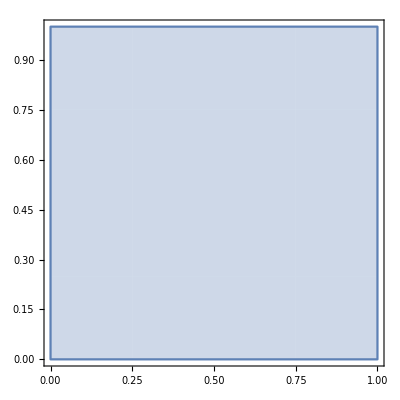

```mathematica
r = 1;
Ω = Rectangle[{0,0},{r,r}];
RegionPlot[Ω]
```

Setting Sound Source Location:

```mathematica
xs = 0.5;
ys = 0.5;
r=1;
```

Creating the Acoustic Model:

```mathematica
monopoleModel2D=AcousticModel[p[x,y],{x,y},ρ,{Q[ω,{x,y},{xs,ys}],{0}}]-(ω^2 p[x,y])/(ρ c^2)
```

Setting a Boundary Condition:

```mathematica
Subscript[Γ, abcf]=NeumannValue[-(((ⅈ ω)/c+1/(2 r)) p[x,y])/ρ,True];
```

Creating the PDE:

```mathematica
pde={monopoleModel2D==Subscript[Γ, abcf]}/.{c->Subscript[c, air],ρ->Subscript[ρ, air]};
```

Solving the PDE:

```mathematica
pfunMonopole2D=ParametricNDSolveValue[pde,p,{x,y}∈Ω,{ω},AcousticsOptions[Subscript[c, air],ω]]
```

Visualizing the Results:

```mathematica
pMonopole500Hz=pfunMonopole2D[2 π f/.{f->500}];
```

## 3D Modeling with Primitive Shapes

The Helmholtz Equation

Creating the Simulation Domain:

```mathematica
Ω = Region[Cone[{{0,0,0},{0,0,2}}, 1]];
RegionPlot3D[Ω]
```

-Graphics3D-

Setting Sound Source Location:

```mathematica
xs = 0;
ys = 0;
zs = 0;
r=1;
```

Creating the Acoustic Model:

```mathematica
monopoleModel3D = AcousticModel[p[x,y,z],{x, y,z}, ρ, {Q[ω,{x,y, z},{xs,ys, zs}],{0}}]-(ω^2 p[x,y,z])/(ρ c^2);
```

Setting a Boundary Condition:

```mathematica
Subscript[Γ, abc]=NeumannValue[-(((ⅈ ω)/c+1/(2 r)) p[x,y,z])/ρ,True];
```

Creating the PDE:

```mathematica
pde = {monopoleModel3D == Subscript[Γ, abc]} /. {c->Subscript[c, air],ρ->Subscript[ρ, air]};
```

Solving the PDE:

```mathematica
pfunMonopole3D = ParametricNDSolveValue[pde,p,{x,y, z}∈omega,{ω},AcousticsOptions[Subscript[c, air],ω]]
```

Visualizing Results:

```mathematica
pMonopole500HzCone = pfunMonopole3D[2π f /. {f->500}];
```

Transcribed as a Function:

```mathematica
(*Will convert above into a function to easily apply to other shapes*)
```

Examples & Tests

```mathematica
(*Grid of Visualizations -- Computer kept crashing :( *)
```

## Depth Map

#### Single-Image Depth Perception Net

Here is an example image from Wolfram:

```mathematica
img=-Graphics-;
```

A neural network exists that can convert an image into a depth map that doesn’t require multi-view reconstruction. It is applied here:

```mathematica
depthMap = NetModel["Single-Image Depth Perception Net Trained on NYU Depth V2 and Depth in the Wild Data"][img];
```

```mathematica
ImageAdjust[Image[depthMap]]
```

-Graphics-

With ListPlot3D, the depthMap can be better visualized.

```mathematica
ListPlot3D[depthMap, PlotStyle->Texture[img]]
```

-Graphics3D-

Notice that some of the depth data has been inaccurately captured. The distance between the farthest point  and the closest point in the image doesn’t appear to be recreated in the depth map. The accuracy of relative positions between the points isn’t maintained.

Fine Tuning the output

We found that multiplying the created depth map by the square root of itself can sometimes yield a more accurate depth map. An example is listed below.

```mathematica
img=-Graphics-;
depthMapModel=NetModel["Single-Image Depth Perception Net Trained on NYU Depth V2 and Depth in the Wild Data"][img];
depthMapModel=Sqrt[Abs[Reverse@depthMapModel]]*(-Reverse@depthMapModel);
ListPlot3D[depthMapModel,PlotStyle->Texture[img],PlotTheme->{"Minimal","NoAxes"},ViewPoint->{0,-0.96,1.84}]
```

-Graphics3D-

We’ve incorporated some post-processing to help improve the accuracy of depth perception here.

#### Creating a Boolean Region

Method 1 - Hexahedrons

A depth map can be re-created into a boolean region by converting each depth map point into a hexahedron, where the depth value is associated with the height of each hexahedron.

```mathematica
depthMap = NetModel["Single-Image Depth Perception Net Trained on NYU Depth V2 and Depth in the Wild Data"][-Graphics-];
```

```mathematica
pts =Table[{{x-1,y-1,-50},{x-1,y,-50},{x,y,-50},{x,y-1,-50},{x-1, y-1 ,depthMap[[x]][[y]]*10},{x-1,y,depthMap[[x]][[y]]*10},{x,y,depthMap[[x]][[y]]*10},{x,y-1,depthMap[[x]][[y]]*10}}, {x, 1, Dimensions[depthMap][[1]], 1}, {y, 1, Dimensions[depthMap][[2]], 1}];
```

```mathematica
pts = Flatten[pts,2];
```

```mathematica
Ω = MeshRegion[pts,Hexahedron[Partition[Range[240*320*8],8]]]
```

-Graphics3D-

Using the mesh region we were able to accurately translate the depth data from an image to a boolean region. We need our data in this format to be compatible with our acoustic model. In order for the mesh region to be compatible with the acoustic model, it needs to fit in a 1 by 1 by 1 region. The method below accomplishes that.

```mathematica
Image2MeshRegion[image_Image,minBound_Integer:0,maxBound_Integer:1]:=Module[
{depthMap,minDepth,maxDepth,inc, width, height, pts},(
If[maxBound≤minBound,Return[]];
depthMap = NetModel["Single-Image Depth Perception Net Trained on NYU Depth V2 and Depth in the Wild Data"][image];
minDepth = Min[depthMap];
maxDepth = Max[depthMap];
depthMap = Rescale[depthMap,{minDepth,maxDepth},{minBound+0.001,maxBound}]; (*the 0.001 is in there to prevent degenerate hexahedrons*)
width = Dimensions[depthMap][[1]];
height = Dimensions[depthMap][[2]];
inc = Divide[maxBound-minBound+0.0,Max[{width,height}]];
pts = Table[{{(x-1)*inc,(y-1)*inc,minBound},{(x-1)*inc,y*inc,minBound},{x*inc,y*inc,minBound},{x*inc,(y-1)*inc,minBound},{(x-1)*inc, (y-1)*inc,depthMap[[x]][[y]]},{(x-1)*inc,y*inc,depthMap[[x]][[y]]},{x*inc,y*inc,depthMap[[x]][[y]]},{x*inc,(y-1)*inc,depthMap[[x]][[y]]}}, {x,  width}, {y, height}];
MeshRegion[Flatten[pts,2],Hexahedron[Partition[Range[width*height*8],8]]]
)]
```

Method 2 - Discretized Region Plot

The depth map can be interpolated into a function and then discretized as shown below.

```mathematica
f = ListInterpolation[Rescale[depthMap,{Min[depthMap],Max[depthMap]},{0.0001,1}], {{0,1}, {0,1}}, InterpolationOrder->{10,10}];
```

```mathematica
rp=RegionPlot3D[z≤f[x,y],{x,0,1},{y,0,1},{z,0,1},PlotPoints->100];
```

```mathematica
DiscretizeGraphics[rp]
```

-Graphics3D-

Examples & Tests

```mathematica
(*Apply the function to different images and put them in a grid*)
```

## 3D Modeling with Depth Maps

Using the Depth Map as the Simulation Domain

Setting Sound Source Location:

```mathematica
xs = 0.1;
ys = 0.1;
zs = 0.1;
r=1;
```

Creating the Acoustic Model:

```mathematica
monopoleModel3D = AcousticModel[p[x,y,z],{x, y,z}, ρ, {Q[ω,{x,y, z},{xs,ys, zs}],{0}}]-(ω^2 p[x,y,z])/(ρ c^2);
```

Setting a Boundary Condition:

```mathematica
Subscript[Γ, abc]=NeumannValue[-(((ⅈ ω)/c+1/(2 r)) p[x,y,z])/ρ,True];
```

Creating the PDE:

```mathematica
pde = {monopoleModel3D == Subscript[Γ, abc]} /. {c->Subscript[c, air],ρ->Subscript[ρ, air]};
```

Solving the PDE:

```mathematica
pfunMonopole3D = ParametricNDSolveValue[pde,p,{x,y, z}∈k,{ω},AcousticsOptions[Subscript[c, air],ω]]
```

ParametricFunction[<>]

```mathematica
k = BoundaryDiscretizeRegion[k];
```

BoundaryDiscretizeRegion::nobrep: There is not a boundary representation that uniquely defines a region with region dimension 2 embedded in dimension 3.

```mathematica
k
```

-Graphics3D-

Visualizing Results:

```mathematica
pMonopole500HzDepthRegion = pfunMonopole3D[2π f /. {f->500}];
```

ParametricNDSolveValue::femnfm: The current version of NDSolve cannot solve equations over boundaries or surfaces. Please specify a region where the embedding dimension is the same as the dimension.

## Audio Processing

Applying the Model to Audio Data